```mathematica
ClearAll["Global`*"];

b={b1,b2,b3};
l={l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11};
t1=0;
t[i_]:=If[i==0,t1,t1+Sum[l[[j]],{j,1,i}]];
(*t[i_]:=If[i==0,0,l[[i]]];*)
g=Length[b];
Aij[i_,j_,k_]:=If[OddQ[i],
(* odd i, continuity condition *)
Switch[i,
(* first row *)
1,Switch[j,
1,Exp[-I k t[1]],
2,-Exp[I k t[1]],
3,-Exp[-I k t[1]],
_,0],
(* next-to-last row *)
2g-1,Switch[j,
2g-2,Exp[I k t[Ceiling[i/2]]],
2g-1,Exp[-I k t[Ceiling[i/2]]],
2g,-Exp[I k t[Ceiling[i/2]]],
_,0],
(* any other odd row *)
_,Switch[j,
i-1,Exp[I k t[Ceiling[i/2]]],
i,Exp[-I k t[Ceiling[i/2]]],
i+1,-Exp[I k t[Ceiling[i/2]]],
i+2,-Exp[-I k t[Ceiling[i/2]]],
_,0]
],
(* even i, derivative condition *)
Switch[i,
2,Switch[j,
1,Exp[-I k t[1]],
2,b[[1]]Exp[I k t[1]],
3,-b[[1]]Exp[-I k t[1]],
_,0],
2g,Switch[j,
2g-2,-Exp[I k t[i/2]],
2g-1,Exp[-I k t[i/2]],
2g,b[[i/2]]Exp[I k t[i/2]],
_,0],
_,Switch[j,
i-2,-Exp[I k t[i/2]],
i-1,Exp[-I k t[i/2]],
i,b[[i/2]]Exp[I k t[i/2]],
i+1,-b[[i/2]]Exp[-I k t[i/2]],
_,0]
]
]
A[k_]:=Table[Aij[i,j,k],{i,1,2g},{j,1,2g}];
A1ij[i_,j_,k_]:=If[i==j==1,-Aij[i,j,k],Aij[i,j,k]];
A1[k_]:=Table[A1ij[i,j,k],{i,1,2g},{j,1,2g}];
R=FullSimplify[Det[A1[k]]/Det[A[k]]]
```

-(((1+b1) (-1+b2) (1+b3) ⅇ^(4 ⅈ k (l1+l2))+(-1+b1) (1+b2) (1+b3) ⅇ^(2 ⅈ k (2 l1+l2))+(-1+b1) (-1+b2) (-1+b3) ⅇ^(2 ⅈ k (2 l1+l2+l3))+(1+b1) (1+b2) (-1+b3) ⅇ^(2 ⅈ k (2 (l1+l2)+l3)))/((-1+b1) (-1+b2) (1+b3) ⅇ^(4 ⅈ k (l1+l2))+(1+b1) (1+b2) (1+b3) ⅇ^(2 ⅈ k (2 l1+l2))+(1+b1) (-1+b2) (-1+b3) ⅇ^(2 ⅈ k (2 l1+l2+l3))+(-1+b1) (1+b2) (-1+b3) ⅇ^(2 ⅈ k (2 (l1+l2)+l3))))

```mathematica
Manipulate[Plot[Abs[R]^2/.{l1->ll1,l2->ll2,l3->ll3,l4->ll4,l5->ll5,l6->ll6,b1->bb1,b2->bb2,b3->bb3,b4->bb4,b5->bb5,b6->bb6},{k,0,kmax},PlotRange->{0,1}],
{ll1,1,10},{ll2,1,10},{ll3,1,10},{ll4,1,10},{ll5,1,10},{ll6,1,10},{bb1,2,10,1},{bb2,2,10,1},{bb3,2,10,1},{bb4,2,10,1},{kmax,2Pi,500}]
```

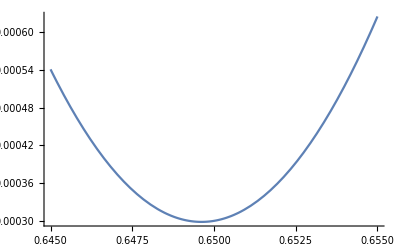

```mathematica
Plot[Abs[R/.{l1->1,l2->2,l3->1,b1->3,b2->2,b3->2}]^2,{k,0.645,0.655}]
```

```mathematica
Manipulate[Abs[R/.{l1->1,l2->2,l3->1,b1->3,b2->2,b3->2,k->kk}],{kk,0.5,1}]
```

```mathematica
Refine[Re[ExpToTrig[R/.{l1->1,l2->2,l3->1,b1->3,b2->2,b3->2}]],Element[k,Reals]]
```

-Re[(18 Cos[8 k]+2 Cos[10 k]+12 Cos[12 k]+12 Cos[14 k]+18 ⅈ Sin[8 k]+2 ⅈ Sin[10 k]+12 ⅈ Sin[12 k]+12 ⅈ Sin[14 k])/(36 Cos[8 k]+4 Cos[10 k]+6 Cos[12 k]+6 Cos[14 k]+36 ⅈ Sin[8 k]+4 ⅈ Sin[10 k]+6 ⅈ Sin[12 k]+6 ⅈ Sin[14 k])]

```mathematica
f[kk_,l_]:=Abs[R]^2/.{l1->1,l2->1,l3->l,b1->2,b2->2,b3->2,k->kk}
```

```mathematica
Minimize[f[x,y],{x,y}]
```

{4.16134×10^-18,{x→2.06168,y→1.}}

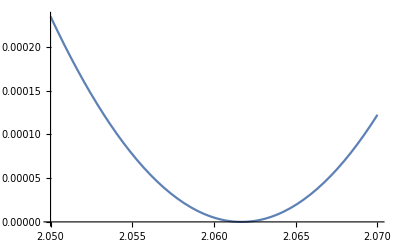

```mathematica
Plot[f[x,1],{x,2.05,2.07}]
```

```mathematica
Minimize[Abs[R]^2/.{l1->1,l2->1,l3->ll,b1->2,b2->2,b3->1,k->kk}//N,{kk,ll}]
```

{1.61762×10^-26,{kk→1.5708,ll→1.02727}}